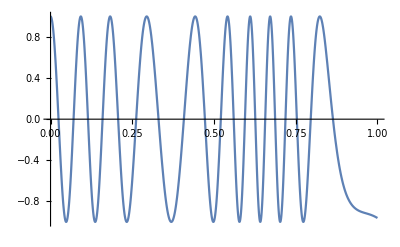

```mathematica
Plot[Cos[2π (10+Sin[10 t])t],{t,0,1}]
```

```mathematica
H=.;H2=({{-2π 13/2 10^3 Sin[2π 60 t], 2π 10^4}, {2π 10^4, 2π 13/2 10^3 Sin[2π 60 t]}});
```

```mathematica
H2//MatrixForm
```

(-13000 π Sin[120 π t] | 20000 π
20000 π | 13000 π Sin[120 π t])

```mathematica
tM=10^-2;
```

```mathematica
pops:=Module[{tSim0,H,ψ,sols,init,p1,p2,p3,p4,p5,c1,c2,c3,c4,c5,SE},
tSim0=tM;
H=H2;
ψ[t_]={c1[t],c2[t]};init=ψ[0]=={1,0};SE=ⅈ ψ'[t]==H.ψ[t];
sols=NDSolve[{SE,init},{c1,c2},{t,tSim0},PrecisionGoal->10,MaxSteps->1000000,Method->"StiffnessSwitching"];
{p1,p2}=Abs[#[t]/.sols]^2&/@{c1,c2}]
```

```mathematica
pops
```

{{Abs[InterpolatingFunction[…][t]]^2},{Abs[InterpolatingFunction[…][t]]^2}}

```mathematica
tab=ParallelTable[{τ,#[[1]]/.t-> τ}&/@pops,Evaluate[{τ,0,tM,1/100 tM}]]ᵀ;
```

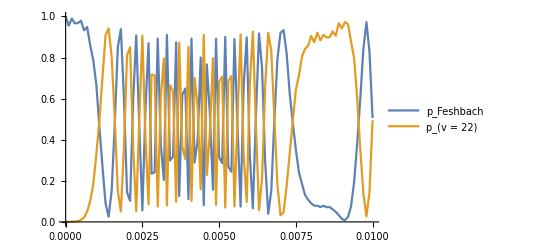

```mathematica
ListPlot[tab,PlotRange->{0,1},Joined->True,PlotLegends->LineLegend[{"p_Feshbach","p_(v = 22)","p_excited","p_ground","p_hf"},LabelStyle->Directive[FontSize->20,FontColor->Gray,FontFamily->"Optima"]],FrameLabel->{"Time (μs)","Population"}]
```